SA20002007郝锐杰

```mathematica
(*无量纲化,引入无量纲参数。教科书上处理谐振子的方法*)
Clear["Global`*"]
α=Sqrt[m*ω/ℏ];
ξ=α*x;
test=Laplacian[ψ[x],{x}]/α^2+(-ξ^2)* ψ[x];
(*     Laplacian[ψ[x],{x}]/α^2+(-ξ^2)* ψ[x]={-E/(0.5ℏω)}*ψ[x]    *)

DEigensystem[{test,DirichletCondition[ψ[x]==0,True]},ψ[x],{x,-∞,∞},4,Assumptions->ℏ>0 && m>0&&ω>0,Method->"Normalize"]
```

{{-1,-3,-5,-7},{(ⅇ^(-(m x^2 ω)/(2 ℏ)) (m ω ℏ)^(1/4))/(π^(1/4) √ℏ),(√2 ⅇ^(-(m x^2 ω)/(2 ℏ)) x ((m ω)/ℏ)^(3/4))/π^(1/4),(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-2+(4 m x^2 ω)/ℏ) (m ω ℏ)^(1/4))/(2 √2 π^(1/4) √ℏ),(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-12 x √((m ω)/ℏ)+8 x^3 ((m ω)/ℏ)^(3/2)) (m ω ℏ)^(1/4))/(4 √3 π^(1/4) √ℏ)}}

```mathematica
qho=-ℏ^2/(2m)Laplacian[ψ[x],{x}]+(m ω^2)/2 x^2 ψ[x];
m=ℏ=ω=1;(*使用自然单位制*)

{v,func}=DEigensystem[{qho,DirichletCondition[ψ[x]==0,True]},ψ[x],{x,-∞,∞},7,Assumptions->ℏ>0 && m>0&&ω>0, Method->"Normalize"](*归一化的波函数*)
```

{{1/2,3/2,5/2,7/2,9/2,11/2,13/2},{(ⅇ^(-x^2/2))/π^(1/4),(√2 ⅇ^(-x^2/2) x)/π^(1/4),(ⅇ^(-x^2/2) (-2+4 x^2))/(2 √2 π^(1/4)),(ⅇ^(-x^2/2) (-12 x+8 x^3))/(4 √3 π^(1/4)),(ⅇ^(-x^2/2) (12-48 x^2+16 x^4))/(8 √6 π^(1/4)),(ⅇ^(-x^2/2) (120 x-160 x^3+32 x^5))/(16 √15 π^(1/4)),(ⅇ^(-x^2/2) (-120+720 x^2-480 x^4+64 x^6))/(96 √5 π^(1/4))}}

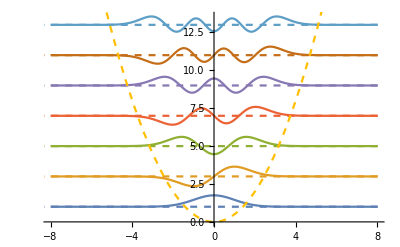

```mathematica
(*将解析求解得到的波函数，画出*)
Show[Plot[Evaluate[ func+v*2],{x,-8,8}],Plot[Evaluate[Append[v*2,1/2 x^2]],{x,-10,10},PlotStyle->Dashed]]
```

```mathematica
(*数值计算*)
(*有限差分处理谐振子势*)
(*当L取10，步长为(1/10^3)前几个本征值与解析结果符合很好。
若L取值过小，如L=1，以及步长过大，导致解析结果偏差很大。
从波函数的图像中可以看出，或者根据谐振子势，可以判断在x->∞时，波函数->0,因此L应尽可能大。
*)
Clear["Global`*"]
qho=-ℏ^2/(2m)Laplacian[ψ[x],{x}]+(m ω^2)/2 x^2 ψ[x];//N
m=ℏ=ω=1;(*使用自然单位制*)//N
L=10;(*从解析结果看，L取10合适*)//N
N0=10000;//N
h=2*L/N0(*步长*)//N
x=Range[-L,L,h];
A=IdentityMatrix[N0+1]*(-2);//N
(A[[#,#+1]]=1)&/@Range[N0];//N
Map[(A[[#,#-1]]=1)&,Range[2,N0+1]];(*获得三对角阵*)//N
MatrixForm[A];
B=IdentityMatrix[N0+1];//N
Map[(B[[#,#]]=1/2*x[[#]]^2)&,Range[N0+1]];
MatrixForm[B];
H=N[-A/(2*h^2)+B];(*得到哈密顿的矩阵形式*)
MatrixForm[H];
val=N[Eigenvalues[H,-5,Method->"Banded"]]
func=N[Eigenvectors[H,-5,Method->"Banded"]];//Timing
```

0.002

{4.49999,3.5,2.5,1.5,0.5}

{114.969,Null}

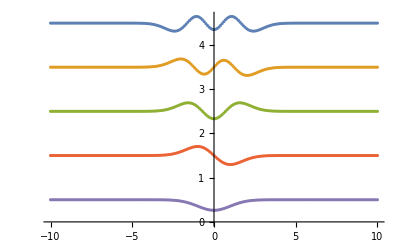

```mathematica
ListPlot[Normalize[func[[#]]]+val[[#]]&/@Range[Length[val]],PlotRange->All,DataRange->{-L,L}]
```

```mathematica
(*Problem 2*)
Clear["Global`*"]
qho=-ℏ^2/(2m)Laplacian[ψ[x],{x}]+((m ω^2)/2 x^2+Cos[x])* ψ[x];
DEigensystem[{qho,DirichletCondition[ψ[x]==0,True]},ψ[x],{x,-∞,∞},3,Assumptions->ℏ>0 && m>0&&ω>0, Method->"Normalize"]
```

DEigensystem[{(1/2 m x^2 ω^2+Cos[x]) ψ[x]-(ℏ^2 ψ''[x])/(2 m),DirichletCondition[ψ[x]==0,True]},ψ[x],{x,-∞,∞},3,Assumptions→ℏ>0&&m>0&&ω>0,Method→Normalize]

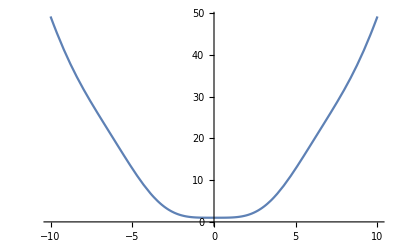

```mathematica
m=ℏ=ω=1;
(*从图中可以看出，在0点附近，简谐效应被破坏*)
Plot[(m ω^2)/2 x^2+Cos[x],{x,-10,10}]
```

```mathematica
Clear["Global`*"]
m=ℏ=ω=1;(*使用自然单位制*)
L=10;
N0=400;
h=2*L/N0(*步长*)//N
x=Range[-L,L,h];
A=IdentityMatrix[N0+1]*(-2);
(A[[#,#+1]]=1)&/@Range[N0];
Map[(A[[#,#-1]]=1)&,Range[2,N0+1]];(*获得三对角阵*)
MatrixForm[A];
B=IdentityMatrix[N0+1];
Map[(B[[#,#]]=Cos[x[[#]]]+1/2*x[[#]]^2)&,Range[N0+1]];
MatrixForm[B];
H=N[-A/(2*h^2)+B];(*得到哈密顿的矩阵形式*)
MatrixForm[H];
val=N[Eigenvalues[H,-5,Method->"Arnoldi"]]
func=N[Eigenvectors[H,-5,Method->"Arnoldi"]];
```

0.05

{4.23103,3.34851,2.52707,1.78961,1.2226}

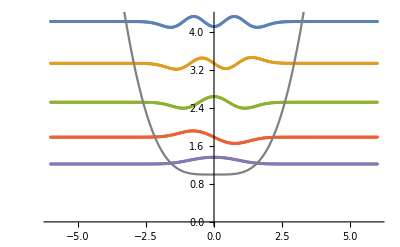

```mathematica
Show[ListPlot[Normalize[func[[#]]]+val[[#]]&/@Range[Length[val]],PlotRange->All,DataRange->{-6,6}],Plot[1/2 a^2+Cos[a],{a,-10,10},PlotStyle->Gray]]
```

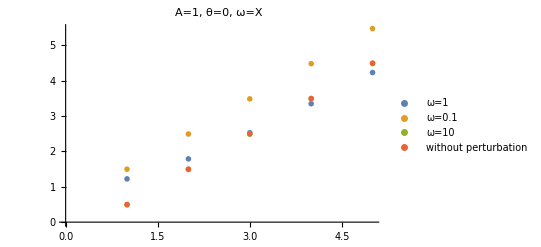

```mathematica
(*探究微扰势中，频率，相位，振幅对本征值的影响*)

w1={4.2310278424554975,3.3485060583819175,2.5270743255317636,1.7896088949547153,1.2226028413830194};
wpoint1={5.474398859797798,4.480599936150045,3.4865036135250933,2.492110077876931,1.4974195150161609};
w10={4.484047939454568,3.4860240963108224,2.487576876374422,1.4887297843539935,0.48950198230663994};
initialvals={4.496794563620567,3.4980457625261367,2.498983947278272,1.4996092650508173,0.49992186278726647};
ListPlot[{Reverse[w1],Reverse[wpoint1],Reverse[w10],Reverse[initialvals]},PlotMarkers->"OpenMarkers",PlotLegends->{"ω=1","ω=0.1","ω=10","without perturbation"},PlotLabel->"A=1, θ=0, ω=X"]
(*从图中可以看出当ω逐渐增大，求得本征值与无微扰势很接近*)
```

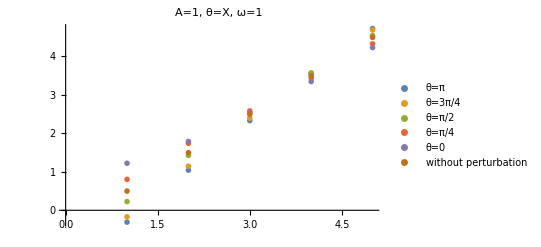

```mathematica
(*不同相位对本征值影响*)

b1={4.725719636668716,3.5584388306569785,2.3315529658871825,1.0429115302138496,-0.30851766772688016};
b2={4.6902129844466485,3.5738967850834893,2.394551523182526,1.147064187083904,-0.1701603172844518};
b3={4.54631384302396,3.5641729335990857,2.5351137858004003,1.4273591660566312,0.22647257412943203};
b4={4.32917253069727,3.4358669915725404,2.584805021069855,1.7419293022814022,0.8037047616689997};
b5={4.2310278424554975,3.3485060583819175,2.5270743255317636,1.7896088949547153,1.2226028413830194};
initialvals={4.496794563620567,3.4980457625261367,2.498983947278272,1.4996092650508173,0.49992186278726647};
ListPlot[{Reverse[b1],Reverse[b2],Reverse[b3],Reverse[b4],Reverse[b5],Reverse[initialvals]},PlotMarkers->"OpenMarkers",PlotLegends->{"θ=π","θ=3π/4","θ=π/2","θ=π/4","θ=0","without perturbation"},PlotLabel->"A=1, θ=X, ω=1"]
(*微扰求解
微扰势具有不同的频率，相位，振幅，其微扰矩阵元中的被积函数具有明显的不同，因此加入余弦函数的微扰势，最终的本征值与微扰势的选取有关。
*)
```

```mathematica
Clear["Global`*"]
α=Sqrt[m*ω/ℏ];
ξ=α*x;
m=ℏ=ω=1;(*使用自然单位制*)
E0[k_]=(k+1/2)*ℏ*ω;

N1[n_]:=Sqrt[α/(2^n*n!*Sqrt[Pi])];(*谐振子势，波函数的归一化系数*)
qho=-ℏ^2/(2m)Laplacian[ψ[x],{x}]+((m ω^2)/2 x^2)* ψ[x];
```

```mathematica
ψ[n_,x_]:=N1[n]*Exp[-α^2*x^2/2]*HermiteH[n,α*x]
Hr=A*Cos[a*x+b];(*以Cos(x)为例*)
A=1;
a=1;
b=3*Pi/4;
H1[n_,k_]:=NIntegrate[ψ[n,x]*Hr*ψ[k,x],{x,-10,10},PrecisionGoal->4,AccuracyGoal->5];
E2[k_]:=Sum[(H1[n,k])^2/(E0[k]-E0[n]),{n,0,k-1}]+Sum[(H1[n,k])^2/(E0[k]-E0[n]),{n,k+1,10}];
En[k_]:=E0[k]+NIntegrate[ψ[k,x]*Hr*ψ[k,x],{x,-10,10}]+E2[k]
```

```mathematica
ValsPertubation=En[#]&/@Range[0,4](*二阶微扰得到的本征值*)
Valsnum={4.2310278424554975,3.3485060583819175,2.5270743255317636,1.7896088949547153,1.2226028413830194};

Reverse[Valsnum](*(*利用数值计算，有限差分，得到的本征值*)*)
```

{-0.223603,1.15888,2.41904,3.59026,4.69693}

{1.2226,1.78961,2.52707,3.34851,4.23103}

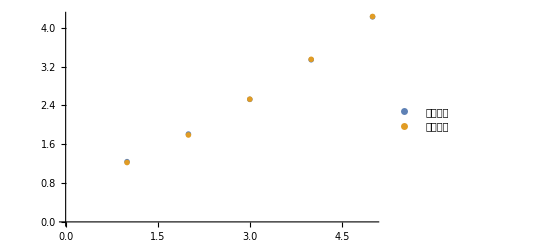

```mathematica
(*从图中可以比较两种计算方法的差距*)
ListPlot[{ValsPertubation,Reverse[Valsnum]},PlotMarkers->"OpenMarkers",PlotLegends->{"二阶微扰","数值计算"}]
```

```mathematica
(*从下图中看出，当微扰势具有不同的频率，不同P的相位，其微扰矩阵元具有明显的不同*)
```

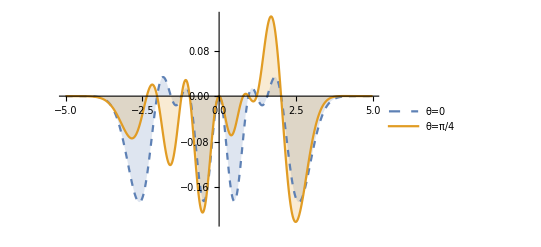

```mathematica
Plot[{ψ[5,x]*Cos[x]*ψ[3,x],ψ[5,x]*Cos[x+Pi/4]*ψ[3,x]},{x,-5,5},PlotStyle->{Dashed,Thick},PlotLegends->{"θ=0","θ=π/4"},Filling->Axis]
```

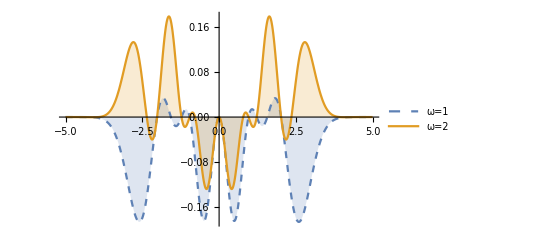

```mathematica
Plot[{ψ[5,x]*Cos[x]*ψ[3,x],ψ[5,x]*Cos[2x]*ψ[3,x]},{x,-5,5},PlotStyle->{Dashed,Thick},PlotLegends->{"ω=1","ω=2"},Filling->Axis]
```

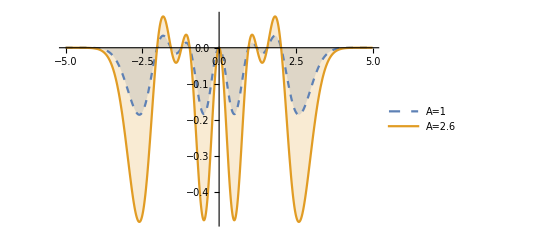

```mathematica
Plot[{ψ[5,x]*Cos[x]*ψ[3,x],ψ[5,x]*2.6*Cos[x]*ψ[3,x]},{x,-5,5},PlotStyle->{Dashed,Thick},PlotLegends->{"A=1","A=2.6"},Filling->Axis]
```

```mathematica
(*Problem 3*)
(*在开始进行计算不规则势之前，先讨论规则方势阱。
-ℏ/(2m)(∂_(x,x) +∂_(y,y))ψ[x,y]=(Subscript[E, x]+Subscript[E, y])ψ[x,y]
Subscript[E, n]=(π^2 ℏ^2)/(2 m)(Subscript[n, x]^2/a^2+Subscript[n, y]^2/b^2),若a=b即为方势阱，存在简并态，如（2,3）=（3,2）
从下面的解析求解以及利用有限差分求解的结果都可以看出存在简并态。
*)
```

```mathematica
Clear["Global`*"]
{vals,funs}=DEigensystem[{-0.5Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Rectangle[],8];
Table[Plot3D[funs⟦i⟧//N//Evaluate,{x,y}∈Rectangle[],PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Classic"],{i,Length[vals]}]
vals//N
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{9.8696,24.674,24.674,39.4784,49.348,49.348,64.1524,64.1524}

```mathematica
Clear["Global`*"]
{vals,funs}=DEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6];
Table[Plot3D[funs⟦i⟧//N//Evaluate,{x,y}∈Disk[],PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Minimal"],{i,Length[vals]}]
vals//N
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{5.78319,14.682,14.682,26.3746,26.3746,30.4713}

```mathematica
(*从最终的结果可以看出，存在简并态，表明有限差分的方法与mathematics内置的解析求解方法的结果一致。可以继续进行不规则势的计算*)
Clear["Global`*"]
L=1;
N0=20;(*格点数,实际数据数要+1*)
h=L/N0
A=IdentityMatrix[(N0+1)^2]*(-4);
(A[[#,#+1]]=1)&/@Range[(N0+1)^2-1];
Map[(A[[#,#-1]]=1)&,Range[2,(N0+1)^2]];(*获得三对角阵*)
(A[[#,#+(N0+1)]]=1)&/@Range[(N0+1)^2-(N0+1)];
(A[[#,#-(N0+1)]]=1)&/@Range[N0+2,(N0+1)^2];
(A[[#,#+1]]=0)&/@Range[N0+1,(N0+1)^2-1,N0+1];(*注意二维中，x维度到达边界时，Subscript[ψ, i+1,j] 这一项为0，即三对角阵中临近对角项，不是所有均为1，存在0*)
(A[[#,#-1]]=0)&/@Range[N0+2,(N0+1)^2,N0+1];
MatrixForm[A];
H=N[-0.5*A/h^2];
MatrixForm[H];
```

1/20

```mathematica
{vals,funcs}=Eigensystem[H,-8,Method->"Arnoldi"];
vals
```

{52.35,52.35,40.2186,40.2186,32.4056,20.2742,20.2742,8.14285}

```mathematica
ArrayReshape[funcs[[-1]],{N0+1,N0+1}];
Table[ListPlot3D[-ArrayReshape[funcs[[-i]],{N0+1,N0+1}],PlotRange->All,PlotLabel->vals⟦-i⟧,PlotTheme->"Classic"],{i,Length[vals]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*Problem 3.1 构建操场势，并将其转换至势能矩阵中*)
Clear["Global`*"]
L=1;
N0=50;(*格点数,实际数据数要+1*)
h=L/N0
A=IdentityMatrix[(N0)^2]*(-4);
(A[[#,#+1]]=1)&/@Range[(N0)^2-1];
Map[(A[[#,#-1]]=1)&,Range[2,(N0)^2]];(*获得三对角阵*)
(A[[#,#+(N0)]]=1)&/@Range[(N0)^2-(N0)];
(A[[#,#-(N0)]]=1)&/@Range[N0+1,(N0)^2];
MatrixForm[A];
H=-A/(2*h^2);
MatrixForm[H];
N[Eigenvalues[N[H],-8,Method->"Arnoldi"]]
```

1/50

{62.209,42.7077,38.7352,38.5968,24.4679,24.4523,18.9839,4.75249}

```mathematica
Clear["Global`*"]
L=4;
N0=50;(*格点数,实际数据数要+1*)
h=L/N0;
(*a矩阵为操场势，并将其转换至势能矩阵中a[i,j]->v[[N0+2-i+(j-1)*(N0+1)]][[N0+2-i+(j-1)*(N0+1)]]或者[v[[i+(j-1)*(N0+1)]][[i+(j-1)*(N0+1)]]等这与步长行走方向有关，但最终结果都相同*)
a=Table[If[-1<=i≤1&&-1<=j≤1||((i-1)^2+j^2)≤1||((i+1)^2+j^2)≤1,0,100000],{j,-L/2,L/2,h},{i,-L/2,L/2,h}];
v=IdentityMatrix[(N0+1)^2];
Table[v[[N0+2-i+(j-1)*(N0+1)]][[N0+2-i+(j-1)*(N0+1)]]=a[[i]][[j]],{i,1,(N0+1)},{j,1,(N0+1)}];
A=IdentityMatrix[(N0+1)^2]*(-4);
(A[[#,#+1]]=1)&/@Range[(N0+1)^2-1];
Map[(A[[#,#-1]]=1)&,Range[2,(N0+1)^2]];(*获得三对角阵*)
(A[[#,#+(N0+1)]]=1)&/@Range[(N0+1)^2-(N0+1)];
(A[[#,#-(N0+1)]]=1)&/@Range[N0+2,(N0+1)^2];
(*注意二维中，y维度到达边界时，Subscript[ψ, i,j+1] 这一项为0，即三对角阵中临近对角项，不是所有均为1，存在0*)
(A[[#,#+1]]=0)&/@Range[N0+1,(N0+1)^2-1,N0+1];(*注意二维中，x维度到达边界时，Subscript[ψ, i+1,j] 这一项为0，即三对角阵中临近对角项，不是所有均为1，存在0*)
(A[[#,#-1]]=0)&/@Range[N0+2,(N0+1)^2,N0+1];
MatrixForm[A];
H=N[-0.5*A/h^2+v];
MatrixForm[H];
```

```mathematica
{vals,funcs}=Eigensystem[H,-8,Method->"Arnoldi"];
vals
```

{9.28715,8.11292,6.4866,6.1637,4.95123,4.21136,2.52761,1.48997}

```mathematica
ArrayReshape[funcs[[-1]],{N0+1,N0+1}];
(*此时求得的特征向量或者波函数为一维向量，需要将其转换为2维向量，才具有物理意义。并画图表示*)
Table[ListPlot3D[-ArrayReshape[funcs[[-i]],{N0+1,N0+1}],PlotRange->All,PlotLabel->vals⟦-i⟧,PlotTheme->"Classic"],{i,Length[vals]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListPointPlot3D[a,PlotTheme->"Classi",PlotRange->All]
```

-Graphics3D-

```mathematica
(*Problem 3.2 构建心形势，与之前的操场势类似*)
Clear["Global`*"]
L=4;
N0=20;(*格点数,实际数据数要+1*)
h=L/N0;
a=Table[If[i^2+(j-(i^2)^(1/3))^2<=1,0,100000],{j,-L/2,L/2,h},{i,-L/2,L/2,h}];
ListPointPlot3D[a,PlotTheme->"Classic",PlotRange->All]
```

-Graphics3D-

```mathematica
(*a矩阵为心形势，并将其转换至势能矩阵中a[i,j]->v[[N0+2-i+(j-1)*(N0+1)]][[N0+2-i+(j-1)*(N0+1)]]或者[v[[i+(j-1)*(N0+1)]][[i+(j-1)*(N0+1)]]等这与步长行走方向有关，但最终结果都相同*)

v=IdentityMatrix[(N0+1)^2];
Table[v[[N0+2-i+(j-1)*(N0+1)]][[N0+2-i+(j-1)*(N0+1)]]=a[[i]][[j]],{i,1,(N0+1)},{j,1,(N0+1)}];
A=IdentityMatrix[(N0+1)^2]*(-4);
(A[[#,#+1]]=1)&/@Range[(N0+1)^2-1];
Map[(A[[#,#-1]]=1)&,Range[2,(N0+1)^2]];(*获得三对角阵*)
(A[[#,#+(N0+1)]]=1)&/@Range[(N0+1)^2-(N0+1)];
(A[[#,#-(N0+1)]]=1)&/@Range[N0+2,(N0+1)^2];
(*注意二维中，y维度到达边界时，Subscript[ψ, i,j+1] 这一项为0，即三对角阵中临近对角项，不是所有均为1，存在0*)
(A[[#,#+1]]=0)&/@Range[N0+1,(N0+1)^2-1,N0+1];(*注意二维中，x维度到达边界时，Subscript[ψ, i+1,j] 这一项为0，即三对角阵中临近对角项，不是所有均为1，存在0*)
(A[[#,#-1]]=0)&/@Range[N0+2,(N0+1)^2,N0+1];
MatrixForm[A];
H=N[-0.5*A/h^2+v];
MatrixForm[H];
```

```mathematica
{vals,funcs}=Eigensystem[H,-8,Method->"Arnoldi"];
vals
```

{16.8989,16.1426,13.3727,11.3509,11.2561,6.93172,6.63689,3.03785}

```mathematica
(*此时求得的特征向量或者波函数为一维向量，需要将其转换为2维向量，才具有物理意义。并画图表示*)
Table[ListPlot3D[-ArrayReshape[funcs[[-i]],{N0+1,N0+1}],PlotRange->All,PlotLabel->vals⟦-i⟧,PlotTheme->"Classic"],{i,Length[vals]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}